### Константы

```mathematica
If[True,
A            =- 0.024 ;
B            = 1.69 ;
CC          = 0.5 ;
α            = 10^-5                (* K^-1 *);
T0          = 300                 (* K *);
Young   = 1.75 * 10^11 (* Па *);
σf          = 1.1 * 10^8     (* Па *);
ϵf          = 0.000628571 ;
l            = 10                    (* Длина стержня *);
Tf          =22                    (* Конечный момент времени *); 
τ            = 0.05               (* Шаг времени *);
a            = 50                    (* Просто константа *);
n            =  10                   (* Число узлов сетки *);
h                                          (* Шаг сетки *);
];
```

### Определение всех необходимых функций

```mathematica
F[x_] := a Sin[(π x)/l];
```

```mathematica
T1[x_, t_] := T0 + F[x]t Sin[t];
T2[ x_, t_ ] := T0 + F[x] Cos[π t^2](t+1);
```

```mathematica
TT = T1;
```

Тепловые деформации

```mathematica
ϵT [T_] := α(T - T0);
```

Полные деформации

```mathematica
ϵ[u_] := D[u, {x, 1}];
```

SetDelayed::write: Tag List in {0.0000747316,0.0000441437,0.0000150528,-9.69333×10^-6,-0.0000276725,-0.0000371247,-0.0000371247,-0.0000276725,-9.69333×10^-6,0}[u_] is Protected.

Аналитическое решение (перемещения)

```mathematica
uAnalytical = 
First[Flatten[
DSolve[{
D[D[u[x,t], {x, 1}]-ϵT[TT[x, t]], {x, 1}]== 0,
u[0, t] == 0, 
u[l, t] == 0
},u[x,t],{x, t}]]
]⟦2⟧ // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

### Численное решение (метод конечных разностей)

```mathematica
f= D[ϵT[TT[x, t]], {x, 1}]
```

(π t Cos[(π x)/10] Sin[t])/20000

Проверки для шага и количества точек (можем выставлять и то, и то)

```mathematica
If[NumberQ[n],
h = l/n, 
If[NumberQ[h],n = IntegerPart[l/h]; h = l/n]
];
```

Составляем разностное уравнение

```mathematica
(d^2 u)/dx^2== f;
```

```mathematica
(Subscript[u, i+1] - 2 Subscript[u, i] + Subscript[u, i-1])/h^2 == f;
```

Создаем массив точек и значений функции f в них, далее решаем СЛАУ: Au = F(f(x_1), ..., f(x_n) ).

```mathematica
points = Table[i*h, {i, 0, n}];
```

```mathematica
yk = Table[0, {i, 0, n}]; ynext = yk;
```

```mathematica
For[k = 0, k < 30, ++k,
	yk =ynext ;
	FF = Table[(Subscript[y, i+1] - 2 Subscript[y, i] + Subscript[y, i-1] + α h (TT[points⟦i⟧, t] - TT[points⟦i+1⟧, t])) *(ⅇ^(-CC/ϵf((Subscript[y, i+1] - Subscript[y, i])/h- α(TT[points⟦i+1⟧, t] - T0)))- ⅇ^(-CC/ϵf((Subscript[y, i] - Subscript[y, i-1])/h- α(TT[points⟦i⟧, t] - T0)))), {i, 1, n-1}] /. {Subscript[y, 0] -> 0, Subscript[y, n] -> 0, t-> 1};
	J = Table[ Table[ ((FF⟦j⟧ /.{ Subscript[y, i] -> (Subscript[y, i] + h)}) - FF⟦j⟧)/h,{i, 1, n-1}],{j, 1, n-1}];
	Replacement = Table[Subscript[y, i] -> yk⟦i⟧, {i, 1, n-1}];
	Y = LinearSolve[J /. Replacement, -FF /. Replacement];
	ynext = yk + {0}~Join~Y~Join~{0};
];
```

General::munfl: Exp[-795.455] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.352] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
FF /.Replacement // MatrixForm
```

(-0.0000141661
-0.000012719
-8.70842×10^-6
-3.81421×10^-6
-4.67541×10^-7
-4.67541×10^-7
-3.81421×10^-6
-8.70842×10^-6
-0.000012719)

```mathematica
J /. Replacement// MatrixForm
```

General::munfl: Exp[-795.455] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-795.352] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(-6.42286026557825×10^345 | -0.999856 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.21084474348013×10^345 | -7.05089301547674×10^345 | -1.10881 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3.52491164462526×10^345 | -7.59266895514611×10^345 | -1.21728 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3.79593094185622×10^345 | -7.96218737122981×10^345 | -1.31088 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3.9808927546941×10^345 | -8.09352526504882×10^345 | -1.37475 | 0 | 0 | 0
0 | 0 | 0 | 0 | -4.04680429809101×10^345 | -7.96186748665778×10^345 | -1.39752 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3.98121263926613×10^345 | -7.59208874615786×10^345 | -1.37486 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3.79651115084447×10^345 | -7.05015141873064×10^345 | -1.31107
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.52565324137136×10^345 | -6.42206612373099×10^345)

```mathematica
ynext
```

{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0}

```mathematica
values = {0}~Join~Table[f/.{ x-> points⟦i⟧}, {i, 1, n-1}]~Join~{0} ;
```

```mathematica
H = Table[
Table[
If [i == j, 
If[i == 0 || i== n, 1,-2/h^2],
If[(i == j-1 || i== j+1)&&j≠ 0 && j≠ n , 1/h^2, 0 ]
]
, {i, 0, n}],
{j, 0, n}
];
```

```mathematica
H // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Численно найденные значения перемещений путем решения ДУ

```mathematica
uNumerical =LinearSolve[H, values] ;
```

Нахождение деформаций (du/dx)

```mathematica
duNumerical = Table[1/h(uNumerical⟦i+1⟧ - uNumerical⟦i⟧), {i, 1, n}] ;
```

### Решение на каждом временном слое

```mathematica
σ = Table[0,{i, 1, n}];
σfv = Table[σf,{i, 1, n}];
ϵ = Table[0,{i, 1, n}]; 
ϵe = Table[0,{i, 1, n}]; 
ϵcrk = Table[0,{i, 1, n}];
T = Table[0,{i, 1, n}];
```

```mathematica
data = {};
For[tt = 0, tt <= Tf, tt = tt+τ,
temp = {};
For [i = 1, i< n, ++i,
T⟦i⟧ = TT[points⟦i⟧, tt] /. t-> tt; 
ϵ⟦i⟧ = duNumerical⟦i⟧ /. t-> tt;
ϵe⟦i⟧ = ϵ⟦i⟧ - ϵT[T⟦i⟧] - ϵcrk⟦i⟧ /. t-> tt;
If[Young*ϵe⟦i⟧<σfv⟦i⟧,
σ⟦i⟧ = Young*ϵe⟦i⟧,
 σfv⟦i⟧ = σf(A + B ⅇ^(-CC  * (ϵ⟦i⟧ - ϵT[T⟦i⟧])/ϵf)); σ⟦i⟧ = σfv⟦i⟧; ϵcrk⟦i⟧ = ϵ⟦i⟧ -  ϵT[T⟦i⟧] - σ⟦i⟧/Young; ϵe⟦i⟧ = (First@Flatten@Solve[σf(A + B ⅇ^(-CC*(x +ϵcrk⟦i⟧)/ϵf))== σfv⟦i⟧, x])⟦2⟧;
];
AppendTo[temp, {tt, T⟦i⟧, σ⟦i⟧, ϵ⟦i⟧, ϵ⟦i⟧ -  ϵT[T⟦i⟧], ϵcrk⟦i⟧}]
];
AppendTo[data, temp]
];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

### Графики

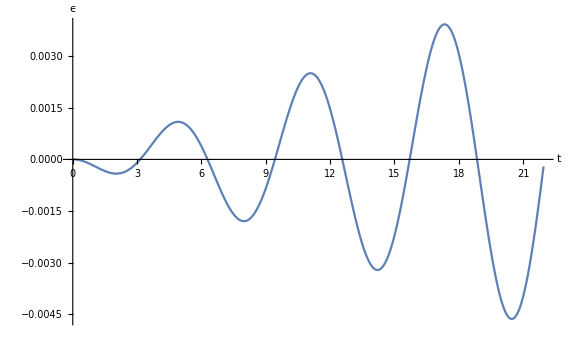

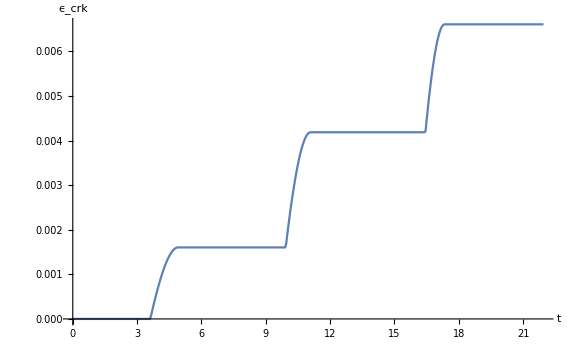

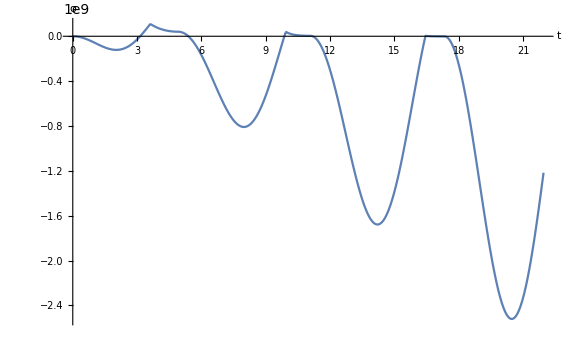

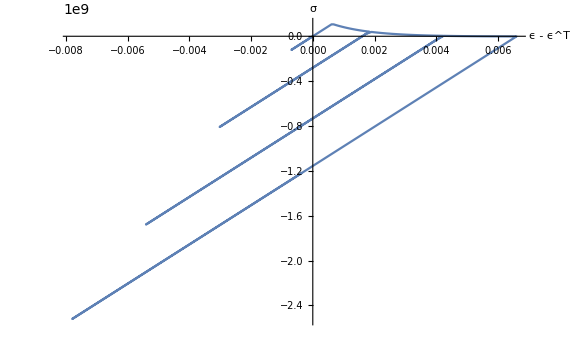

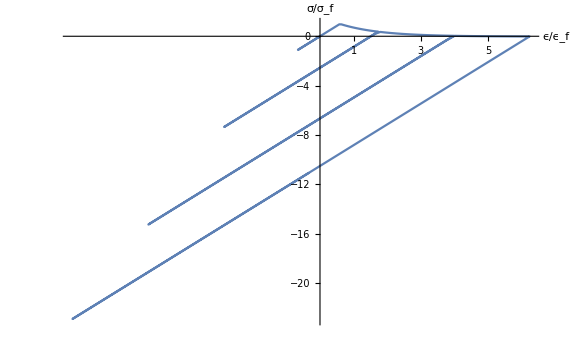

```mathematica
tϵ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 4⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"},AxesStyle->Black]
tϵcrk = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, -1⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"},AxesStyle->Black]
tσ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"},AxesStyle->Black]
dϵσ = ListPlot[Table[{data⟦i, 2, 5⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"},AxesStyle->Black]
normdϵσ = ListPlot[Table[{data⟦i, 2, 4⟧/ϵf, data⟦i, 2, 3⟧/σf}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"},AxesStyle->Black]




tT = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 2⟧}, {i, 1,IntegerPart@ (Tf/τ)}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"},AxesStyle->Black ];
```

### Сохраняем графики

```mathematica
If[False, 
SetDirectory[NotebookDirectory[]];
options =StringJoin[ToString@TT~StringJoin~"/", StringJoin["h_", ToString[h] ~StringJoin~"_"], StringJoin["tau_", ToString[τ]]];
With[
{directory=FileNameJoin[{ParentDirectory@NotebookDirectory[], StringJoin["LaTeX/pic/",options ]}]},
Switch[FileType[directory],
None,CreateDirectory[directory],
Directory, Print["Overriding files in directory: "~StringJoin~directory]
];
Export[FileNameJoin[{directory, "epsilon(t).pdf"}], tϵ];
Export[FileNameJoin[{directory, "epsilon_crk(t).pdf"}], tϵcrk];
Export[FileNameJoin[{directory, "sigma(t).pdf"}], tσ];
Export[FileNameJoin[{directory, "sigma(epsilon).pdf"}], dϵσ];
Export[FileNameJoin[{directory, "norm_sigma(epsilon).pdf"}], normdϵσ];
Export[FileNameJoin[{directory, "T(t).pdf"}], tT];
]
];
```